```mathematica
Clear["Global`*"]
ClearAll["Global`*"] 
<<Notation`
Off[Symbolize::bsymbexs]


Symbolize[Subscript[u, ρ]]; Symbolize[Subscript[u, ϕ]]; Symbolize[Subscript[u, ζ]];
Symbolize[u^ρ]; Symbolize[u^ϕ]; Symbolize[u^ζ];
Symbolize[w^ρ]; Symbolize[w^ϕ]; Symbolize[w^ζ];
Symbolize[Subscript[w, ρ]]; Symbolize[Subscript[w, ϕ]]; Symbolize[Subscript[w, ζ]];
 Symbolize[N^𝔄]Symbolize[N^𝔅]Symbolize[N^ℭ];Symbolize[N^𝔇]Symbolize[N^𝔈]Symbolize[N^𝔉];
Symbolize[Subscript[a, ρ,𝔄]];Symbolize[Subscript[a, ϕ,𝔅]];Symbolize[Subscript[a, ζ,ℭ]];
Symbolize[Subscript[b, ρ,𝔇]];Symbolize[Subscript[b, ϕ,𝔈]];Symbolize[Subscript[b, ζ,𝔉]]
Symbolize[L̄];
 Notation[g_(i_·j_·)   ⟺  CoVarMetricCoeffs[[i_,j_]]]
Notation[g^(i_·j_·)   ⟺  ContraVarMetricCoeffs[[i_,j_]]]
Notation[Γ_(i_·j_·)^(k_·)   ⟺  Γ[[i_,j_,k_]]]
Notation[w^(i_·)   ⟺  ContraVarDispW[[i_]]]
Notation[u^(i_·)   ⟺  ContraVarDispU[[i_]]]
Notation[u_(i_·)   ⟺  CoVarDispU[[i_]]]
Notation[x^(i_·)   ⟺  Coords[[i_]]]
Notation[w_(j_·)   ⟺  CoVarDispW[[j_]]]
Notation[u^(i_·)|_(j_·)  ⟺  CovariantDU1[i_,j_]]
Notation[u_(i_·)|_(j_·)  ⟺  CovariantDU2[i_,j_]]
Notation[w^(i_·)|_(j_·)  ⟺  CovariantDW1[i_,j_]]
Notation[w_(i_·)|_(j_·)  ⟺  CovariantDW2[i_,j_]]
Notation[γ_(i_·j_·)   ⟺  StrainCovariantU[[i_,j_]]]
Notation[ϵ_(i_·j_·)   ⟺  StrainCovariantW[[i_,j_]]]
Notation[𝔼^(i_·j_·k_·l_·)   ⟺  StiffnessContra[[i_,j_,k_,l_]]]
Notation[(∂u_)/(∂x_)   ⟺  D[u_,x_]]
Notation[τ^(i_·j_·)   ⟺  StressContra[[i_,j_]]]
Patt={
 x_[ρ,ζ] Derivative[0,1][(y_)][ρ,ζ],
x_[ρ,ζ] Derivative[1,0][(y_)][ρ,ζ],Derivative[1,0][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[0,1][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ]
x_[ρ,ζ] y_[ρ,ζ]};




<<HaneeshPackages`
PrntRls={Subscript[u, 1]-> Subscript[u,1],Subscript[u, 2]-> Subscript[u,2],Subscript[u, 3]-> Subscript[u,3],
Subscript[x, 1]-> Subscript[x,1],Subscript[x, 2]-> Subscript[x,2],Subscript[x, 3]-> Subscript[x,3],
u^ρ-> Superscript[u,ρ],u^ϕ-> Superscript[u,ϕ],u^ζ-> Superscript[u,ζ],
Subscript[u, ρ]-> Subscript[u,ρ],Subscript[u, ϕ]-> Subscript[u,ϕ],Subscript[u, ζ]-> Subscript[u,ζ],
N^𝔄-> Superscript[N,𝔄],N^𝔅-> Superscript[N,𝔅],N^ℭ-> Superscript[N,ℭ],
N^𝔇-> Superscript[N,𝔇],N^𝔈-> Superscript[N,𝔈],N^𝔉-> Superscript[N,𝔉],
Subscript[a, ρ, 𝔄]-> Subscript[a,ρ,𝔄],Subscript[a, ϕ, 𝔅]-> Subscript[a,ϕ,𝔅],Subscript[a, ζ, ℭ]-> Subscript[a,ζ,ℭ],
Subscript[b, ρ, 𝔇]-> Subscript[b,ρ,𝔇],Subscript[b, ϕ, 𝔈]-> Subscript[b,ϕ,𝔈],Subscript[b, ζ, 𝔉]-> Subscript[b,ζ,𝔉],
Subscript[w, ρ]-> Subscript[w,ρ],Subscript[w, ϕ]-> Subscript[w,ϕ],Subscript[w, ζ]-> Subscript[w,ζ],
L̄->Overscript[L,_],Subscript[ΔT, 0]-> Subscript[ΔT,0]
};
Pprint[expri_]:=Module[{expr=expri},
expr/.PrntRls//MatrixForm//pdConv
];
```

```mathematica
CoVarMetricCoeffs={{1,0,0},{0,ρ^2+(L̄)^2,L̄},{0,L̄,1}};
ContraVarMetricCoeffs={{1,0,0},{0,1/ρ^2,-(L̄)/ρ^2},{0,-(L̄)/ρ^2,(ρ^2+(L̄)^2)/ρ^2}};

Γ=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Γ[[;;,;;,1]]={{0,0,0},{0,-ρ,0},{0,0,0}};
Γ[[;;,;;,2]]={{0,1/ρ,0},{1/ρ,0,0},{0,0,0}};
Γ[[;;,;;,3]]={{0,-(L̄)/ρ,0},{-(L̄)/ρ,0,0},{0,0,0}};
Table[g_(i·j·),{i,1,3},{j,1,3}]//Pprint
Table[g^(i·j·),{i,1,3},{j,1,3}]//Pprint
```

(1 | 0 | 0
0 | (L̄)^2+ρ^2 | L̄
0 | L̄ | 1)

(1 | 0 | 0
0 | 1/ρ^2 | -(L̄)/ρ^2
0 | -(L̄)/ρ^2 | ((L̄)^2+ρ^2)/ρ^2)

```mathematica
Coords={ρ,ϕ,ζ};
ContraVarDispU={Subscript[a, ρ,𝔄](N^𝔄)[ρ,ζ],Subscript[a, ϕ,𝔅](N^𝔅)[ρ,ζ],Subscript[a, ζ,ℭ](N^ℭ)[ρ,ζ]}; 
ContraVarDispW={Subscript[b, ρ,𝔇](N^𝔇)[ρ,ζ],Subscript[b, ϕ,𝔈](N^𝔈)[ρ,ζ],Subscript[b, ζ,𝔉](N^𝔉)[ρ,ζ]}; 
CoVarDispU=Table[∑_(j=1)^3 (g_(i·j·)u^(j·)),{i,1,3}];
CoVarDispW=Table[∑_(j=1)^3 (g_(i·j·)w^(j·)),{i,1,3}];


Table[x^(i·),{i,1,3}]//Pprint
Table[u_(i·),{i,1,3}]//Pprint
Table[u^(i·),{i,1,3}]//Pprint
Table[w_(i·),{i,1,3}]//Pprint
Table[w^(i·),{i,1,3}]//Pprint
```

(ρ
ϕ
ζ)

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
((L̄)^2+ρ^2) a_(ϕ,𝔅) N^𝔅(ρ,ζ)+L̄ a_(ζ,ℭ) N^ℭ(ρ,ζ)
L̄ a_(ϕ,𝔅) N^𝔅(ρ,ζ)+a_(ζ,ℭ) N^ℭ(ρ,ζ))

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
a_(ϕ,𝔅) N^𝔅(ρ,ζ)
a_(ζ,ℭ) N^ℭ(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
((L̄)^2+ρ^2) b_(ϕ,𝔈) N^𝔈(ρ,ζ)+L̄ b_(ζ,𝔉) N^𝔉(ρ,ζ)
L̄ b_(ϕ,𝔈) N^𝔈(ρ,ζ)+b_(ζ,𝔉) N^𝔉(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
b_(ϕ,𝔈) N^𝔈(ρ,ζ)
b_(ζ,𝔉) N^𝔉(ρ,ζ))

```mathematica
CovariantDU2[i_,j_]:=((∂u_(i·))/(∂x^(j·))-∑_(k=1)^3 (u_(k·)Γ_(i·j·)^(k·)));
StrainCovariantU=Table[1/2((u_(i·)|_(j·))+(u_(j·)|_(i·))),{i,1,3},{j,1,3}];
Flatten@FullSimplify@Table[γ_(i·j·),{i,1,3},{j,1,3}]//Pprint
```

(a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
ρ a_(ρ,𝔄) N^𝔄(ρ,ζ)
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))
1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))
L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))

```mathematica
CovariantDW2[i_,j_]:=((∂w_(i·))/(∂x^(j·))-∑_(k=1)^3 (w_(k·)Γ_(i·j·)^(k·)));
StrainCovariantW=Table[1/2((w_(i·)|_(j·))+(w_(j·)|_(i·))),{i,1,3},{j,1,3}];
Flatten@FullSimplify@Table[ϵ_(i·j·),{i,1,3},{j,1,3}]//Pprint
```

(b_(ρ,𝔇) (∂N^𝔇(ρ,ζ))/(∂ρ)
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
1/2 (L̄ b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+b_(ρ,𝔇) (∂N^𝔇(ρ,ζ))/(∂ζ)+b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
ρ b_(ρ,𝔇) N^𝔇(ρ,ζ)
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ζ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ζ))
1/2 (L̄ b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+b_(ρ,𝔇) (∂N^𝔇(ρ,ζ))/(∂ζ)+b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ζ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ζ))
L̄ b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ζ)+b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ζ))

```mathematica
StiffnessContra=μ Table[g^(i·r·) g^(j·s·)+g^(i·s·) g^(j·r·)+λ/μ g^(i·j·)g^(r·s·),{i,1,3},{j,1,3},{r,1,3},{s,1,3}];
```

```mathematica
StressContra=Table[∑_(r=1)^3 ∑_(s=1)^3 𝔼^(i·j·r·s·)(γ_(r·s·)-αΔT g_(r·s·)),{i,1,3},{j,1,3}];
```

```mathematica
W=FullSimplify@Sum[τ^(i·j·)ϵ_(i·j·),{i,1,3},{j,1,3}];
```

```mathematica
FullSimplify[W]//Pprint
```

(μ (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ) a_(ϕ,𝔅) b_(ϕ,𝔈) (L̄)^4)/ρ^2+(μ (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ) a_(ϕ,𝔅) b_(ζ,𝔉) (L̄)^3)/ρ^2+(μ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ) a_(ζ,ℭ) b_(ϕ,𝔈) (L̄)^3)/ρ^2+(μ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ) a_(ζ,ℭ) b_(ζ,𝔉) (L̄)^2)/ρ^2+2 μ (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ) a_(ϕ,𝔅) b_(ϕ,𝔈) (L̄)^2+μ (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ) a_(ϕ,𝔅) b_(ϕ,𝔈) (L̄)^2+μ (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ) a_(ϕ,𝔅) b_(ζ,𝔉) L̄+μ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ) a_(ζ,ℭ) b_(ϕ,𝔈) L̄+μ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ) a_(ζ,ℭ) b_(ϕ,𝔈) L̄-(2 μ (∂N^𝔈(ρ,ζ))/(∂ζ) a_(ρ,𝔄) b_(ϕ,𝔈) N^𝔄(ρ,ζ) L̄)/ρ-3 αΔT λ (∂N^𝔉(ρ,ζ))/(∂ζ) b_(ζ,𝔉)-2 αΔT μ (∂N^𝔉(ρ,ζ))/(∂ζ) b_(ζ,𝔉)+λ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ) a_(ζ,ℭ) b_(ζ,𝔉)+2 μ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ) a_(ζ,ℭ) b_(ζ,𝔉)+λ (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ζ) a_(ρ,𝔄) b_(ζ,𝔉)+μ (∂N^𝔉(ρ,ζ))/(∂ρ) ((∂N^ℭ(ρ,ζ))/(∂ρ) a_(ζ,ℭ)+(∂N^𝔄(ρ,ζ))/(∂ζ) a_(ρ,𝔄)+(∂N^𝔅(ρ,ζ))/(∂ρ) L̄ a_(ϕ,𝔅)) b_(ζ,𝔉)-3 αΔT λ (∂N^𝔇(ρ,ζ))/(∂ρ) b_(ρ,𝔇)-2 αΔT μ (∂N^𝔇(ρ,ζ))/(∂ρ) b_(ρ,𝔇)+μ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ζ) a_(ζ,ℭ) b_(ρ,𝔇)+λ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ρ) a_(ζ,ℭ) b_(ρ,𝔇)+λ (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ρ) a_(ρ,𝔄) b_(ρ,𝔇)+2 μ (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ρ) a_(ρ,𝔄) b_(ρ,𝔇)+(μ (∂N^𝔄(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ζ) (ρ^2+(L̄)^2) a_(ρ,𝔄) b_(ρ,𝔇))/ρ^2+μ ρ^2 (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ) a_(ϕ,𝔅) b_(ϕ,𝔈)+μ ρ^2 (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ) a_(ϕ,𝔅) b_(ϕ,𝔈)+(λ (∂N^𝔉(ρ,ζ))/(∂ζ) a_(ρ,𝔄) b_(ζ,𝔉) N^𝔄(ρ,ζ))/ρ+(λ (∂N^𝔇(ρ,ζ))/(∂ρ) a_(ρ,𝔄) b_(ρ,𝔇) N^𝔄(ρ,ζ))/ρ+(b_(ρ,𝔇) (ρ (-3 αΔT λ+(∂N^ℭ(ρ,ζ))/(∂ζ) a_(ζ,ℭ) λ+(∂N^𝔄(ρ,ζ))/(∂ρ) a_(ρ,𝔄) λ-2 αΔT μ-2 μ (∂N^𝔅(ρ,ζ))/(∂ζ) L̄ a_(ϕ,𝔅))+(λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ)) N^𝔇(ρ,ζ))/ρ^2

Global Stiffness Matrix and Force Vector
K U =F
𝔄∈{1, N_nodes}, 𝔅={ N_nodes+1, 2 N_nodes}, 𝔅={ 2 N_nodes+1, 3 N_nodes}
𝔇∈{1, N_nodes}, 𝔈={ N_nodes+1, 2 N_nodes}, 𝔉={ 2 N_nodes+1, 3 N_nodes}

Global Stiffness Matrix

```mathematica
K=Simplify@Outer[D[W ρ^3,#1,#2]&,{Subscript[a, ρ,𝔄],Subscript[a, ϕ,𝔅],Subscript[a, ζ,ℭ]},{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Flatten@Table[Collect[Expand@K[[i,j]],Patt,Simplify],{i,1,3},{j,1,3}]//Pprint
```

(μ ρ ((L̄)^2+ρ^2) (∂N^𝔄(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ζ)+ρ^3 (λ+2 μ) (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ρ)+ρ (λ+2 μ) N^𝔄(ρ,ζ) N^𝔇(ρ,ζ)+λ ρ^2 N^𝔄(ρ,ζ) (∂N^𝔇(ρ,ζ))/(∂ρ)+λ ρ^2 N^𝔇(ρ,ζ) (∂N^𝔄(ρ,ζ))/(∂ρ)
-2 μ ρ^2 L̄ N^𝔄(ρ,ζ) (∂N^𝔈(ρ,ζ))/(∂ζ)
λ ρ^3 (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ζ)+λ ρ^2 N^𝔄(ρ,ζ) (∂N^𝔉(ρ,ζ))/(∂ζ)+μ ρ^3 (∂N^𝔄(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ρ)
-2 μ ρ^2 L̄ N^𝔇(ρ,ζ) (∂N^𝔅(ρ,ζ))/(∂ζ)
μ ρ ((L̄)^2+ρ^2)^2 (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ)+μ ρ^3 ((L̄)^2+ρ^2) (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ)
μ ρ^3 L̄ (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ρ)+μ ρ L̄ ((L̄)^2+ρ^2) (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ)
λ ρ^3 (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ρ)+λ ρ^2 N^𝔇(ρ,ζ) (∂N^ℭ(ρ,ζ))/(∂ζ)+μ ρ^3 (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ζ)
μ ρ^3 L̄ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ)+μ ρ L̄ ((L̄)^2+ρ^2) (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ)
(μ ρ (L̄)^2+ρ^3 (λ+2 μ)) (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ)+μ ρ^3 (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ρ))

Global Force Vector

```mathematica
F=Simplify@Map[D[(W ρ^3/.{Subscript[a, ρ,𝔄]->0,Subscript[a, ϕ,𝔅]->0,Subscript[a, ζ,ℭ]->0}),#]&,{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Flatten@Table[Collect[Expand@F[[i]],Patt,Simplify],{i,1,3}]//Pprint
```

(-αΔT ρ^2 (3 λ+2 μ) (N^𝔇(ρ,ζ)+ρ (∂N^𝔇(ρ,ζ))/(∂ρ))
0
-αΔT ρ^3 (3 λ+2 μ) (∂N^𝔉(ρ,ζ))/(∂ζ))

```mathematica
Symbolize[Ω^n];
Symbolize[J^e];
Symbolize[j^e];
Symbolize[Subscript[η, g]];
Symbolize[Ι^e];
Symbolize[Subscript[n, el]] (*number of elements*);
Symbolize[Subscript[n, np]] (*numbet of nodal points*);
Symbolize[Subscript[n, en]] (*number of element nodes*);
Symbolize[Subscript[n, dof]] (*number of degrees of freedom*);
Symbolize[Subscript[n, guass]] (*number of degrees of freedom*);
Symbolize[N^(1)];Symbolize[N_(,ξ)^(1)];Symbolize[N_(,η)^(1)];Symbolize[N_(,ρ)^(1)];Symbolize[N_(,ζ)^(1)];
Symbolize[N^(2)];Symbolize[N_(,ξ)^(2)];Symbolize[N_(,η)^(2)];Symbolize[N_(,ρ)^(2)];Symbolize[N_(,ζ)^(2)];
Symbolize[N^(3)];Symbolize[N_(,ξ)^(3)];Symbolize[N_(,η)^(3)];Symbolize[N_(,ρ)^(3)];Symbolize[N_(,ζ)^(3)];
Symbolize[N^(i)];
Symbolize[Subscript[x, i_]];
Symbolize[Subscript[y, i_]];
Symbolize[Subscript[w, i_]];
Symbolize[Subscript[ξ, i_]];
Symbolize[Subscript[η, i_]];
Symbolize[Subscript[f, i_]];
<<NDSolve`FEM`
Guass=N@{{1/6,{1/6,1/6}},
{1/6,{2/3,1/6}},{1/6,{1/6,2/3}}};

(N^(1))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[1]];
(N^(2))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[2]];
(N^(3))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[3]];
(N_(,ξ)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],ξ];
(N_(,η)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],η];
(N_(,ξ)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],ξ];
(N_(,η)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],η];
(N_(,ξ)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],ξ];
(N_(,η)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],η];
```

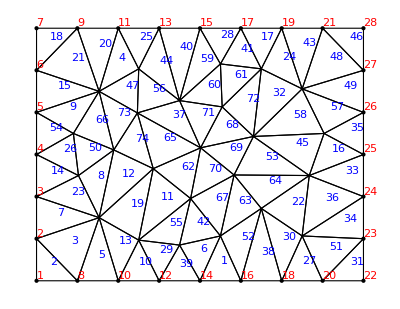

```mathematica
λ=1; μ=1; (*Linear Elastic Properties*)
αΔT=1;(*Thermal Loading*)

Subscript[ρ, 0]=0.25;Subscript[ρ, 1]=1;
Subscript[ζ, 0]=0.0;Subscript[ζ, 1]=0.58;
Ω^n=ToElementMesh[Rectangle[{Subscript[ρ, 0],Subscript[ζ, 0]},{Subscript[ρ, 1],Subscript[ζ, 1]}],MaxCellMeasure->0.01,"MeshElementType"->"TriangleElement","MeshOrder"->1];
Show[(Ω^n)["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]],
(Ω^n)["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]]]
```

```mathematica
(*Clear[Coordinates,IEN,Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, np]]*)
Coordinates=(Ω^n)["Coordinates"];
IEN=Apply[List,(Ω^n)["MeshElements"],{1}][[1,1]]ᵀ ;
Subscript[n, en]=Dimensions[IEN][[1]];
Subscript[n, el]=Dimensions[IEN][[2]];
Subscript[n, np]=Length@Coordinates;
Subscript[n, dof]=3;
```

RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] or RowBox[{StyleBox["f", "TI"], "/@", StyleBox["expr", "TI"]}] applies StyleBox["f", "TI"] to each element on the first level in StyleBox["expr", "TI"]. 
RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Map", "[", StyleBox["f", "TI"], "]"}] represents an operator form of Map that can be applied to an expression.

```mathematica
ScalarIntegration[f0_]:=Module[{f=f0,Subscript[x, 1]=0.0,Subscript[x, 2]=0.,Subscript[x, 3]=0.,Subscript[y, 1]=0.0,Subscript[y, 2]=0.,Subscript[y, 3]=0.,P,Q,R,J^e=0.0,Ι^e=0.,Ι=0.,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i]},

For[e=1,e≤ Subscript[n, el],e++,
{P,Q,R}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}=Coordinates[[{P,Q,R}]];
J^e=(-Subscript[x, 2] Subscript[y, 1]+Subscript[x, 3] Subscript[y, 1]+Subscript[x, 1] Subscript[y, 2]-Subscript[x, 3] Subscript[y, 2]-Subscript[x, 1] Subscript[y, 3]+Subscript[x, 2] Subscript[y, 3]);(*Jacobian Determinant*)

For[i=1;Ι^e=0.0,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]}}=Guass[[i]];
Subscript[x, i]=(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 3];
Subscript[y, i]=(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 3];
Ι^e+=Subscript[w, i] f[Subscript[x, i],Subscript[y, i]];
];
Ι+=J^e Ι^e
];
Ι
]
```

```mathematica
ElementForceVector[e0_]:=Module[{e=e0,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],P,Q,R,j^e,J^e,Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i],Subscript[f, i],Subscript[w, i],Ι^e,Ι},
{P,Q,R}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}=Coordinates[[{P,Q,R}]];
j^e=-Subscript[x, 2] Subscript[y, 1]+Subscript[x, 3] Subscript[y, 1]+Subscript[x, 1] Subscript[y, 2]-Subscript[x, 3] Subscript[y, 2]-Subscript[x, 1] Subscript[y, 3]+Subscript[x, 2] Subscript[y, 3];(*Jacobian Determinant*)
J^e={{-Subscript[x, 1]+Subscript[x, 2],-Subscript[y, 1]+Subscript[y, 2]},{-Subscript[x, 1]+Subscript[x, 3],-Subscript[y, 1]+Subscript[y, 3]}};
({{(N_(,ρ)^(1))[ξ_,η_], (N_(,ρ)^(2))[ξ_,η_], (N_(,ρ)^(3))[ξ_,η_]}, {(N_(,ζ)^(1))[ξ_,η_], (N_(,ζ)^(2))[ξ_,η_], (N_(,ζ)^(3))[ξ_,η_]}})= Inverse[J^e].({{(N_(,ξ)^(1))[ξ,η], (N_(,ξ)^(2))[ξ,η], (N_(,ξ)^(3))[ξ,η]}, {(N_(,η)^(1))[ξ,η], (N_(,η)^(2))[ξ,η], (N_(,η)^(3))[ξ,η]}})//Simplify;
For[i=1;Ι^e=0.0,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]}}=Guass[[i]];
Subscript[x, i]=(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 3];
Subscript[y, i]=(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 3];
Subscript[f, i]={-αΔT(3λ+2μ)(Subscript[x, i])^2{(N^(1))[Subscript[ξ, i],Subscript[η, i]]+Subscript[x, i] (N_(,ρ)^(1))[Subscript[ξ, i],Subscript[η, i]],(N^(2))[Subscript[ξ, i],Subscript[η, i]]+Subscript[x, i] (N_(,ρ)^(2))[Subscript[ξ, i],Subscript[η, i]],(N^(3))[Subscript[ξ, i],Subscript[η, i]]+Subscript[x, i] (N_(,ρ)^(3))[Subscript[ξ, i],Subscript[η, i]]},{0,0,0},
-αΔT(3λ+2μ)(Subscript[x, i])^3{(N_(,ζ)^(1))[Subscript[ξ, i],Subscript[η, i]],(N_(,ζ)^(2))[Subscript[ξ, i],Subscript[η, i]],(N_(,ζ)^(3))[Subscript[ξ, i],Subscript[η, i]]}
};
Ι^e+=Subscript[w, i] Subscript[f, i]
];
Ι^e
]
```

```mathematica
ID=Table[0,{i,1,Subscript[n, dof]},{j,1,Subscript[n, np]}];
P=1;
For[A=1,A≤ Subscript[n, np],A++,
For[i=1,i≤ Subscript[n, dof],i++,
If[!MemberQ[Subscript[η, g][[i]],A],ID[i,A]=P;P=P+1,ID[i,A]=0];
];
]
```

Set::write: Tag List in {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»}}[1,1] is Protected.

Set::write: Tag List in {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»}}[2,1] is Protected.

Set::write: Tag List in {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2»}}[3,1] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

```mathematica
Subscript[n, dof]
```

n_dof

```mathematica
Subscript[n, np]
```

n_np

```mathematica
Subscript[n, np]=Length@Coordinates
```

52

```mathematica
?For
```

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.

```mathematica
ID
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Subscript[η, g]={{},{1,8,12},{1,8,12}}
```

{{},{1,8,12},{1,8,12}}

```mathematica
η={{1,2},{1,2},{3,4}};
Format[η[[i_]]]:=Subscript[η, Subscript[g, i]]
```

Part::pkspec1: The expression i_ cannot be used as a part specification.

SetDelayed::write: Tag Part in MakeBoxes[{{1,2},{1,2},{3,4}}⟦i_⟧,FormatType_] is Protected.

SetDelayed::write: Tag Part in {{1,2},{1,2},{3,4}}⟦i_⟧ is Protected.

$Failed

```mathematica
?Format
```

RowBox[{"Format", "[", StyleBox["expr", "TI"], "]"}] prints as the formatted form of StyleBox["expr", "TI"]. Assigning values to RowBox[{"Format", "[", StyleBox["expr", "TI"], "]"}] defines print forms for expressions. 
RowBox[{"Format", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"]}], "]"}] gives a format for the specified form of output.

```mathematica
1.0 ∈{1.0}
```

1.∈{1.}

```mathematica
If
```

True

```mathematica
!MemberQ[{1,2,3},3]
```

False